# Math 385 HW # 7

## Mario L. Gutierrez Abed

(1) Use the function f(x)=1/(1+x^2)  on [-2,2]. Then

a) Plot a Bezier curve on this interval (Split it into two Bezier curves, one in [-2,0] and the other one on [0,2] ).

Solution:
We need to find a parametric cubic (Bezier) curve in the form β(t)=(1-t)^3 B_00+3(t(1-t))^2 B_01+3t^2(1-t)B_02+t^3 B_03 . 

In order to use this curve we need to determine the coefficients. The starting and ending points are simply  
▸ B_00=(x_0,f(x_0)) 
▸ B_03=(x_f,f(x_f)), 
where x_0 is the initial point and x_f is the ending point. 
To find the other two coefficients we need to do a bit of arithmetic...
▸ B'_00=ⅆ/ⅆx(x_0,f(x_0))=(1,f'(x_0))=3(B_01-B_00)
⟹(1,f'(x_0))=3 B_01-3B_00⟹ B_01=B_00+1/3(1,f'(x_0))
▸ B'_03=ⅆ/ⅆx(x_f,f(x_f))=(1,f'(x_f))=3(B_03-B_02)
⟹(1,f'(x_f))=3 B_03-3B_02⟹ B_02=B_03-1/3(1,f'(x_f))

Now that we have a way to determine the coefficients, let’s define and plot the curve...

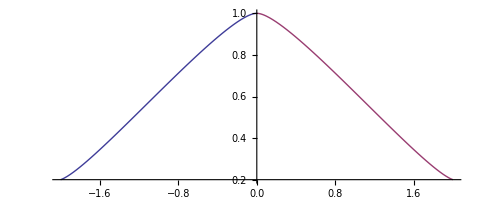

```mathematica
f[x_]=1/(1+x^2);
g[x_]=D[f[x],x];
Subscript[x, 01]=-2;Subscript[x, f1]=0;Subscript[x, 02]=0;Subscript[x, f2]=2;

Subscript[β, 00]={Subscript[x, 01],f[Subscript[x, 01]]};
Subscript[β, 01]={Subscript[β, 00]⟦1⟧+1/3,Subscript[β, 00]⟦2⟧+1/3*g[Subscript[x, 01]]};
Subscript[β, 03]={Subscript[x, f1],f[Subscript[x, f1]]};
Subscript[β, 02]={Subscript[β, 03]⟦1⟧-1/3,Subscript[β, 03]⟦2⟧-1/3*g[Subscript[x, f1]]};
xcoord1=(1-t)^3*Subscript[β, 00]⟦1⟧+3 t*(1-t)^2*Subscript[β, 01]⟦1⟧+3 t^2*(1-t)*Subscript[β, 02]⟦1⟧+t^3*Subscript[β, 03]⟦1⟧;
ycoord1=(1-t)^3*Subscript[β, 00]⟦2⟧+3 t*(1-t)^2*Subscript[β, 01]⟦2⟧+3 t^2*(1-t)*Subscript[β, 02]⟦2⟧+t^3*Subscript[β, 03]⟦2⟧;

Subscript[β, 10]={Subscript[x, 02],f[Subscript[x, 02]]};
Subscript[β, 11]={Subscript[β, 10]⟦1⟧+1/3,Subscript[β, 10]⟦2⟧+1/3*g[Subscript[x, 02]]};
Subscript[β, 13]={Subscript[x, f2],f[Subscript[x, f2]]};
Subscript[β, 12]={Subscript[β, 13]⟦1⟧-1/3,Subscript[β, 13]⟦2⟧-1/3*g[Subscript[x, f2]]};
xcoord2=(1-t)^3*Subscript[β, 10]⟦1⟧+3 t*(1-t)^2*Subscript[β, 11]⟦1⟧+3 t^2*(1-t)*Subscript[β, 12]⟦1⟧+t^3*Subscript[β, 13]⟦1⟧;
ycoord2=(1-t)^3*Subscript[β, 10]⟦2⟧+3 t*(1-t)^2*Subscript[β, 11]⟦2⟧+3 t^2*(1-t)*Subscript[β, 12]⟦2⟧+t^3*Subscript[β, 13]⟦2⟧;

bezier=ParametricPlot[{{xcoord1,ycoord1},{xcoord2,ycoord2}},{t,0,1}]
```

b) Plot all three functions (B_1,B_2,f(x)) on the same graph .

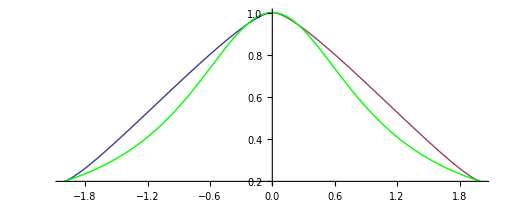

```mathematica
myfunction=Plot[f[x],{x,-2,2},PlotStyle->Green];
Show[bezier,myfunction]
```

(2) Use the function γ(x)=x^2 ⅇ^-x-1/10 on the interval x∈[3,8]. Then construct a third degree polynomial ℓ(x) using the least squares fitting method using the points
x_i=4,5,6,7. Lastly, plot ℓ(x)  and γ(x) on the same graph on the interval [3,8]. 

Solution:
We want a third degree polynomial using the least squares fitting method. 
Given a polynomial in the form a x^3+b x^2+c x+d, the distance from this curve to the data points is given by ||(x_i,y_i)-(x_i,a x_i^3+b x_i^2+c x_i+d)||. In order to get rid of the absolute value, we will square each of the terms and add them to get a function σ with independent variables a,b,c,d. Hence we have 
                              σ(a,b,c,d)=∑_i [y_i-(a x_i^3+b x_i^2+c x_i+d)]^2
Now we apply standard max/min techniques to σ by differentiating with respect to each of the independent variables :

ⅆσ/ⅆa=∑_i 2 [y_i-(a x_i^3+b x_i^2+c x_i+d)](-x_i^3)
       =2∑_i [a x_i^6+b x_i^5+c x_i^4+(d-y_i)x_i^3]

ⅆσ/ⅆb=∑_i 2 [y_i-(a x_i^3+b x_i^2+c x_i+d)](-x_i^2)
      =2∑_i [a x_i^5+b x_i^4+c x_i^3+(d-y_i)x_i^2]

ⅆσ/ⅆc=∑_i 2 [y_i-(a x_i^3+b x_i^2+c x_i+d)](-x_i)
      =2∑_i [a x_i^4+b x_i^3+c x_i^2+(d-y_i)x_i]

ⅆσ/ⅆd=∑_i 2 [y_i-(a x_i^3+b x_i^2+c x_i+d)](-1)
      =2∑_i [a x_i^3+b x_i^2+c x_i+d-y_i]
      
Now we set all these equations equal to zero and set up a system of linear equations to solve a,b,c,and d :
		0=2∑_i [a x_i^6+b x_i^5+c x_i^4+(d-y_i)x_i^3]
		0=2∑_i [a x_i^5+b x_i^4+c x_i^3+(d-y_i)x_i^2]
		0=2∑_i [a x_i^4+b x_i^3+c x_i^2+(d-y_i)x_i]
		0=2∑_i [a x_i^3+b x_i^2+c x_i+d-y_i]

A bit of arithmetic yields
		0=a∑_i x_i^6+b∑_i x_i^5+c∑_i x_i^4+d∑_i x_i^3-∑_i x_i^3 y_i
		0=a∑_i x_i^5+b∑_i x_i^4+c∑_i x_i^3+d∑_i x_i^2-∑_i y_i x_i^2
		0=a∑_i x_i^4+b ∑_i x_i^3+c ∑_i x_i^2+d∑_i x_i-∑_i y_i x_i
		0=a∑_i x_i^3+b∑_i x_i^2+c∑_i x_i-∑_i y_i+n d

From the above we have 
		∑_i x_i^3 y_i=a∑_i x_i^6+b∑_i x_i^5+c∑_i x_i^4+d∑_i x_i^3
		∑_i y_i x_i^2=a∑_i x_i^5+b∑_i x_i^4+c∑_i x_i^3+d∑_i x_i^2
		∑_i y_i x_i=a∑_i x_i^4+b ∑_i x_i^3+c ∑_i x_i^2+d∑_i x_i
		∑_i y_i=a∑_i x_i^3+b∑_i x_i^2+c∑_i x_i+n d
		
In matrix form we have

(∑_i x_i^3 y_i
∑_i y_i x_i^2
∑_i y_i x_i
∑_i y_i) = (∑_i x_i^6 | ∑_i x_i^5 | ∑_i x_i^4 | ∑_i x_i^3
∑_i x_i^5 | ∑_i x_i^4 | ∑_i x_i^3 | ∑_i x_i^2
∑_i x_i^4 | ∑_i x_i^3 | ∑_i x_i^2 | ∑_i x_i
∑_i x_i^3 | ∑_i x_i^2 | ∑_i x_i | n)(a
b
c
d)

From this point on we can solve for a,b,c, and d in several different ways. What I’ll do is the following:

I’ll define mymat and myvec as follows

mymat=(∑_i x_i^6 | ∑_i x_i^5 | ∑_i x_i^4 | ∑_i x_i^3
∑_i x_i^5 | ∑_i x_i^4 | ∑_i x_i^3 | ∑_i x_i^2
∑_i x_i^4 | ∑_i x_i^3 | ∑_i x_i^2 | ∑_i x_i
∑_i x_i^3 | ∑_i x_i^2 | ∑_i x_i | n)

 myvec=(∑_i x_i^3 y_i
∑_i y_i x_i^2
∑_i y_i x_i
∑_i y_i)
 
 Then we have that 
 
 (a
b
c
d)=Inverse[mymat] . myvec
 
 Let’s get on with the computations...

```mathematica
γ[x_]=x^2*ⅇ^-x-1/10;
mypts={4,5,6,7};
funcpts={γ[4],γ[5],γ[6],γ[7]};

coeff1=Sum[(mypts⟦i⟧)^6,{i,Length[mypts]}];
coeff2=Sum[(mypts⟦i⟧)^5,{i,Length[mypts]}];
coeff3=Sum[(mypts⟦i⟧)^4,{i,Length[mypts]}];
coeff4=Sum[(mypts⟦i⟧)^3,{i,Length[mypts]}];
coeff5=Sum[(mypts⟦i⟧)^2,{i,Length[mypts]}];
coeff6=Sum[mypts⟦i⟧,{i,Length[mypts]}];

ycoeff1=Sum[(mypts⟦i⟧)^3*funcpts⟦i⟧,{i,Length[mypts]}];
ycoeff2=Sum[(mypts⟦i⟧)^2*funcpts⟦i⟧,{i,Length[mypts]}];
ycoeff3=Sum[mypts⟦i⟧*funcpts⟦i⟧,{i,Length[mypts]}];
ycoeff4=Sum[funcpts⟦i⟧,{i,Length[mypts]}];

mymat=({{coeff1, coeff2, coeff3, coeff4}, {coeff2, coeff3, coeff4, coeff5}, {coeff3, coeff4, coeff5, coeff6}, {coeff4, coeff5, coeff6, Length[mypts]}});
myvec=({{ycoeff1}, {ycoeff2}, {ycoeff3}, {ycoeff4}});
coefficients=Inverse[mymat].myvec;

finaleq=coefficients⟦1⟧*x^3+coefficients⟦2⟧*x^2+coefficients⟦3⟧*x+coefficients⟦4⟧;
ℓ[x_]=finaleq⟦1⟧;
ℓ[x]//Together
```

1/(30 ⅇ^7)(-29400+75600 ⅇ-63000 ⅇ^2+16800 ⅇ^3-3 ⅇ^7+18130 x-44820 ⅇ x+35250 ⅇ^2 x-8560 ⅇ^3 x-3675 x^2+8640 ⅇ x^2-6375 ⅇ^2 x^2+1440 ⅇ^3 x^2+245 x^3-540 ⅇ x^3+375 ⅇ^2 x^3-80 ⅇ^3 x^3)

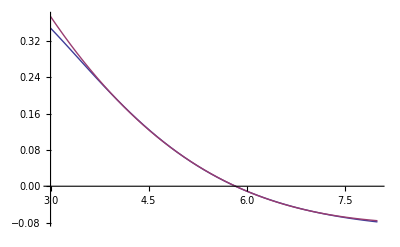

```mathematica
Plot[{γ[x],ℓ[x]},{x,3,8}]
```

Very good fit, it was worth all the work !! :)